```mathematica
games={1,3,5,7};

single64={{0.82,31.62,54.97},
{0.81,24.08,41.15},
{0.77,19.42,31.19},
{0.73,16.26,25.57}};

double64={{0.83,29.56,47.05},
{0.76,21.61,31.56},
{0.72,17.97,24.74},
{0.68,15.81,21.14}};

doubleext64={{0.81,28.70,47.21},
{0.75,20.42,30.15},
{0.71,16.68,23.35},
{0.67,14.45,19.09}};

roundrobin64={{0.60,14.60,17.83},
{0.53,11.45,13.23},
{0.50,10.11,11.54},
{0.47,9.16,10.42}};
```

```mathematica
data={single64,double64,doubleext64,roundrobin64};
```

```mathematica
datat=Transpose/@data;
```

```mathematica
<<"PlotLegends`"
```

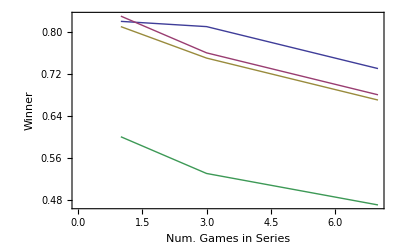

```mathematica
ListLinePlot[({games,#[[1]]}//Transpose)&/@datat,PlotLegend->{"Single","Double","DoubleExt","RoundRobin"},LegendShadow->None,LegendPosition->{1,-.25},FrameLabel->{"Num. Games in Series","Winner"},Frame->{{True,False},{True,False}},Axes->False]
```

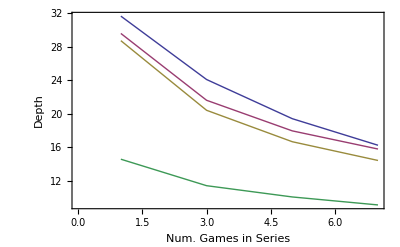

```mathematica
ListLinePlot[({games,#[[2]]}//Transpose)&/@datat,PlotLegend->{"Single","Double","DoubleExt","RoundRobin"},LegendShadow->None,LegendPosition->{1,-.25},FrameLabel->{"Num. Games in Series","Depth"},Frame->{{True,False},{True,False}},Axes->False]
```

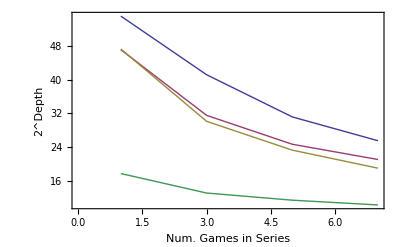

```mathematica
ListLinePlot[({games,#[[3]]}//Transpose)&/@datat,PlotLegend->{"Single","Double","DoubleExt","RoundRobin"},LegendShadow->None,LegendPosition->{1,-.25},FrameLabel->{"Num. Games in Series","2^Depth"},Frame->{{True,False},{True,False}},Axes->False]
```